```mathematica
4-Oscillator Transduction
```

```mathematica
Shoumik Chowdhury  3/11/2020
```

```mathematica
Preliminaries
```

```mathematica
Id[n_]:=IdentityMatrix[n] 
mJn[n_]:=ArrayFlatten[Id[n]⊗({{0, 1}, {-1, 0}})] ; (* Symplectic matrix in QP basis *)
mJqqn[n_] :=ArrayFlatten[({{0, 1}, {-1, 0}})⊗Id[n]]; (*Symplectic matrix in QQ basis *)
sympQn[mS_, n_]:=1-Norm[mSᵀ.mJn[n].mS-mJn[n]]; (* Test for symplecticity *)

n = 8; (* For a 4-mode transducer we work with n = 8 *)
mJ = mJn[n];
sympQ[mS_] := sympQn[mS, n]
```

#### Helper Functions

```mathematica
({{Note that "⟦{1,7,2,8,3,9,4,10,5,11,6,12}, {1,7,2,8,3,9,4,10,5,11,6,12}⟧" converts from "qqpp" -> "qpqp"}, {Meanwhile "⟦{1,3,5,7,9,11,2,4,6,8,10,12}, {1,3,5,7,9,11,2,4,6,8,10,12}⟧" converts "qpqp" -> "qqpp".}})
```

```mathematica
QQtoQP[n0_, M0_] :=
(* Converts a matrix from QQ basis to QP basis*) 
Module[{n=n0, M=M0},
	ord= Flatten[Table[{i, n+i}, {i, 1, n}]];
	Return[M⟦ord, ord⟧]
]

QPtoQQ[n0_, M0_] := 
(* Converts a matrix from QP basis to QQ basis*)
Module[{n=n0, M=M0},
	odds = Table[{i}, {i, 1, 2n, 2}];
	evens = Table[{i+1}, {i, 1, 2n, 2}];
	ord = Flatten[Join[odds,evens]];
	Return[M⟦ord, ord⟧]
] 

(*Generate random n×n symplectic matrix in QQ basis and convert to QP*)
rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_, n_]:=QQtoQP[n, Id[2n]-Inverse[(mJqqn[n].rSymMat[{a,b},2n]+1/2 Id[2n])]]; 
(*Generate random local operations for n = 6*)
randomLocal[a_, b_] := ArrayFlatten[({{rSympMat[a,b, 1], 0, 0, 0, 0, 0}, {0, rSympMat[a,b, 1], 0, 0, 0, 0}, {0, 0, rSympMat[a,b, 1], 0, 0, 0}, {0, 0, 0, rSympMat[a,b, 1], 0, 0}, {0, 0, 0, 0, rSympMat[a,b, 1], 0}, {0, 0, 0, 0, 0, rSympMat[a,b, 1]}})];
```

```mathematica
Theory
```

References:"Cavity Optomechanics" (https: //arxiv.org/abs/1303.0733) and KL paper (https: //www.nature.com/articles/nphys2911)
Hamiltonian given by   (a⃗)^†.H.a⃗, where  a⃗ = {a_o, a_m, a_μ, a_o^†, a_m^†, a_μ^†} and  (a⃗)^†= {(a_o)^†,(a_m)^†,(a_μ)^†,a_o,a_m,a_μ}
H = 1/2(Δ_o | g_om | 0 | 0 | g_om | 0
g_om | ω_m | g_μm | g_om | 0 | g_μm
0 | g_μm | Δ_μ | 0 | g_μm | 0
0 | g_om | 0 | Δ_o | g_om | 0
g_om | 0 | g_μm | g_om | ω_m | g_μm
0 | g_μm | 0 | 0 | g_μm | Δ_μ) := (A | B
B^† | P)
Linearized Hamiltonian:H=Δ_o ((a_o)^† a_o+1/2)+Δ_μ ((a_μ)^† a_μ+1/2)+ω_m ((a_m)^† a_m+1/2)+g_om (a_o+(a_o)^†) (a_m+(a_m)^†)+g_μm (a_μ+(a_μ)^†) (a_m+(a_m)^†)   
Langevin Eq: d/dt (a
a^†)= I [(a | a^†)H(a
a^†), (a
a^†)] - 1/2(κ | 0
0 | κ)(a
a^†)+(√κ | 0
0 | √κ)(A_in
A_in^†) (*1mode example *)
Fourier Transform: â[ω] ∝∫â(t) e^(-I ω t)dt       and     (â[-ω])^† ∝∫â (t)^† e^(-I ω t)dt
Langevin → (I ω | □
□ | Iω)(a[ω]
a[-ω]^†)= I(-A^⋆-P | -B^†
B^ᵀ | A+P^⋆)(a[ω]
a[-ω]^†)- 1/2(κ | 0
0 | κ)(a[ω]
a[-ω]^†) + (√κ | 0
0 | √κ)(A_in[ω]
A_in[-ω]^†)
Thus →    T(a[ω]
a[-ω]^†) = Y(A_in[ω]
A_in[-ω]^†); then extend this to a[-ω] and a[ω]^†modes to get full matrix
Input Output relation: A_out[ω] = A_in[ω] - √κ a[ω]; gives matrix equations (A⃗)_out[ω] = (A⃗)_in[ω] - W(M^-1 W  (A⃗)_in)= S_complex(A⃗)_in

```mathematica
Setup and Initialization
```

```mathematica
T[ω_] := I({{ω, 0, 0, 0, 0, 0, 0, 0}, {0, ω, 0, 0, 0, 0, 0, 0}, {0, 0, ω, 0, 0, 0, 0, 0}, {0, 0, 0, ω, 0, 0, 0, 0}, {0, 0, 0, 0, ω, 0, 0, 0}, {0, 0, 0, 0, 0, ω, 0, 0}, {0, 0, 0, 0, 0, 0, ω, 0}, {0, 0, 0, 0, 0, 0, 0, ω}}) - I({{- Subscript[Δ, o]+I Subscript[κ, o]/2, -Subscript[g, om], 0, 0, 0, -Conjugate[Subscript[g, om]]/2, 0, 0}, {-Conjugate[Subscript[g, om]], - ωm+I Subscript[κ, m]/2, -Subscript[g, μm], 0, -Conjugate[Subscript[g, om]]/2, 0, -Conjugate[Subscript[g, μm]]/2, 0}, {0, -Conjugate[Subscript[g, μm]], - Subscript[Δ, μ]+I Subscript[κ, μ]/2, -Subscript[g, μb], 0, -Conjugate[Subscript[g, μm]]/2, 0, -Conjugate[Subscript[g, μb]]/2}, {0, 0, -Conjugate[Subscript[g, μb]], - Subscript[Δ, b]+I Subscript[κ, b]/2, 0, 0, -Conjugate[Subscript[g, μb]]/2, 0}, {0, Subscript[g, om]/2, 0, 0, Subscript[Δ, o]+ I Subscript[κ, o]/2, Conjugate[Subscript[g, om]], 0, 0}, {Subscript[g, om]/2, 0, Subscript[g, μm]/2, 0, Subscript[g, om], ωm+I Subscript[κ, m]/2, Conjugate[Subscript[g, μm]], 0}, {0, Subscript[g, μm]/2, 0, Subscript[g, μb]/2, 0, Subscript[g, μm], Subscript[Δ, μ]+ I Subscript[κ, μ]/2, Conjugate[Subscript[g, μb]]}, {0, 0, Subscript[g, μb]/2, 0, 0, 0, Subscript[g, μb], Subscript[Δ, b]+ I Subscript[κ, b]/2}})
```

```mathematica
M[ω_] := ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten
```

```mathematica
Y = ({{√Subscript[κ, o], 0, 0, 0, 0, 0, 0, 0}, {0, √Subscript[κ, m], 0, 0, 0, 0, 0, 0}, {0, 0, √Subscript[κ, μ], 0, 0, 0, 0, 0}, {0, 0, 0, √Subscript[κ, b], 0, 0, 0, 0}, {0, 0, 0, 0, √Subscript[κ, o], 0, 0, 0}, {0, 0, 0, 0, 0, √Subscript[κ, m], 0, 0}, {0, 0, 0, 0, 0, 0, √Subscript[κ, μ], 0}, {0, 0, 0, 0, 0, 0, 0, √Subscript[κ, b]}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
```

```mathematica
Setting values
```

```mathematica
{Subscript[Δ, o], ωm, Subscript[Δ, μ], Subscript[Δ, b], Subscript[κ, o], Subscript[κ, m], Subscript[κ, μ], Subscript[κ, b]} = {3, 1, 7, 5, 1, 1, 1, 1} (*kHz -> Hz*)
{Subscript[g, om],Subscript[g, μm], Subscript[g, μb],Subscript[g, ob]} = {19, 23, 17, 0}  (*Hz*)
```

{3,1,7,5,1,1,1,1}

{19,23,17,0}

```mathematica
Finding Scattering Matrices
```

```mathematica
SComplex= Id[16] - W.Inverse[M[ω]].W ;
```

We want to change from basis A to basis B
(A) ao[+ω], am[+ω],aμ[+ω], ab[+ω],(ao[-ω])^†,(am[-ω])^†,(aμ[-ω])^†,ao[-ω],am[-ω],aμ[-ω], ...
(B) qo[+ω], po[+ω],qm[+ω], pm[+ω], qμ[+ω], pμ[+ω],qb[+ω], pb[+ω],qo[-ω], po[-ω], ...

```mathematica
U = 1/(√2)({{1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I}, {0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
(S = Inverse[U].SComplex.U);
```

```mathematica
Dimensions[S]
```

{16,16}

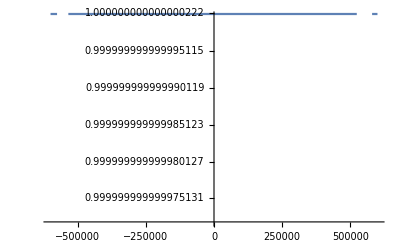

```mathematica
Plot[N[sympQ[S/.{ω->x}]] , {x, -600000., 600000.}](* evaluate this numerically? *)
```

#### Symplectic Decoupling Algorithm

#### Part 1: Code to Decouple the first quadrature

```mathematica
Decouple1Q[mS0_, n0_, c0_, r0_] := 
(*This is a wrapper function to compute the local operations given input mS. We rotate column c -> row r *) 
Module[{mS = mS0, n=n0, c=c0, r =r0},
(* Tabular representations of column vector cv and row vectow rv in qpqp basis *)
cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2n, 2}];
rv=Table[{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2n, 2}];
(*we are going to rotate column c -> row r*)

ncv=Norm/@cv  /. 0 -> 1; (*list of norms of cv*)
nrv=Norm/@rv /. 0 -> 1;(*list of norms of rv*)
mL=Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}] /. ({{0, 0}, {0, 0}}) -> ({{1, 0}, {0, 1}}); 
(*List of local symplectic operations for all modes*)

mSL1qq=ArrayFlatten[({{DiagonalMatrix[mL⟦;;,1,1⟧], DiagonalMatrix[mL⟦;;,1,2⟧]}, {DiagonalMatrix[mL⟦;;,2,1⟧], DiagonalMatrix[mL⟦;;,2,2⟧]}})]; (*this gives a result in qqpp*)

mSL1 = QQtoQP[n, mSL1qq];
Return[mSL1]
]
```

```mathematica
Part 2: Code to Decouple the second quadrature
```

```mathematica
(* INSERT THE CODE HERE *)
```

```mathematica
Part 3: Running the algorithm!
```

```mathematica
mS = S  /. {ω -> 2.};
mSL1 = Decouple1Q[mS, n,13,13];
mS1 = Re[mS.mJ.mSL1.mS];
{sympQ[mSL1], sympQ[mS1]}
Eigenvalues[mSL1.Transpose[mSL1]]
(Chop[N[mS1], 10^-5]) // MatrixForm
```

{1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(-0.00640735 | -0.38515 | 0.352141 | -0.00104074 | 0.769652 | 0.248816 | -1.20439 | -0.325845 | -0.70209 | 0.190792 | 0.227033 | 0.00943047 | 0 | 0 | -0.891821 | 0.327228
0.38515 | -0.00640735 | 0.00104074 | 0.352141 | -0.248816 | 0.769652 | 0.325845 | -1.20439 | 0.190792 | 0.70209 | 0.00943047 | -0.227033 | 0 | 0 | 0.327228 | 0.891821
0.352141 | -0.00104074 | 0.84868 | -0.193555 | -0.283709 | -0.109877 | 0.446994 | 0.148804 | 0.256824 | -0.0170441 | -0.0821792 | -0.002049 | 0 | 0 | 0.323412 | -0.136505
0.00104074 | 0.352141 | 0.193555 | 0.84868 | 0.109877 | -0.283709 | -0.148804 | 0.446994 | -0.0170441 | -0.256824 | -0.002049 | 0.0821792 | 0 | 0 | -0.136505 | -0.323412
0.769652 | 0.248816 | -0.283709 | -0.109877 | 0.404898 | -0.228384 | 0.928639 | 0.236142 | 0.541252 | -0.146938 | -0.175194 | 0.0484662 | 0 | 0 | 0.689278 | -0.241624
-0.248816 | 0.769652 | 0.109877 | -0.283709 | 0.228384 | 0.404898 | -0.236142 | 0.928639 | -0.146938 | -0.541252 | 0.0484662 | 0.175194 | 0 | 0 | -0.241624 | -0.689278
-1.20439 | -0.325845 | 0.446994 | 0.148804 | 0.928639 | 0.236142 | -0.47372 | -0.560886 | -0.857021 | 0.216978 | 0.276702 | -0.0631898 | 0 | 0 | -1.07814 | 0.45968
0.325845 | -1.20439 | -0.148804 | 0.446994 | -0.236142 | 0.928639 | 0.560886 | -0.47372 | 0.216978 | 0.857021 | -0.0631898 | -0.276702 | 0 | 0 | 0.45968 | 1.07814
0.70209 | 0.190792 | -0.256824 | -0.0170441 | -0.541252 | -0.146938 | 0.857021 | 0.216978 | 1.46884 | -0.23144 | -0.168997 | -0.104453 | 0 | 0 | 0.661438 | -0.060423
0.190792 | -0.70209 | -0.0170441 | 0.256824 | -0.146938 | 0.541252 | 0.216978 | -0.857021 | 0.23144 | 1.46884 | 0.104453 | -0.168997 | 0 | 0 | 0.060423 | 0.661438
-0.227033 | 0.00943047 | 0.0821792 | -0.002049 | 0.175194 | 0.0484662 | -0.276702 | -0.0631898 | -0.168997 | -0.104453 | 1.04462 | -0.0154237 | 0 | 0 | -0.195409 | 0.0534693
0.00943047 | 0.227033 | -0.002049 | -0.0821792 | 0.0484662 | -0.175194 | -0.0631898 | 0.276702 | 0.104453 | -0.168997 | 0.0154237 | 1.04462 | 0 | 0 | -0.0534693 | -0.195409
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0.891821 | 0.327228 | -0.323412 | -0.136505 | -0.689278 | -0.241624 | 1.07814 | 0.45968 | 0.661438 | -0.060423 | -0.195409 | 0.0534693 | 0 | 0 | 1.74621 | -0.633548
0.327228 | -0.891821 | -0.136505 | 0.323412 | -0.241624 | 0.689278 | 0.45968 | -1.07814 | 0.060423 | 0.661438 | -0.0534693 | -0.195409 | 0 | 0 | 0.633548 | 1.74621)

```mathematica
newSC =U.mS1.Inverse[U];
newM = Inverse[Id[16]-newSC];
Im[Chop[N[newM⟦1;;8, 1;;8⟧], 10^-10]] // MatrixForm
```

(51.186 | -32.0237 | 34.3419 | 5.01378 | 29.5946 | -13.3236 | 0 | 20.6348
-32.0237 | 26.0224 | -22.0329 | -3.57133 | -19.7887 | 11.4017 | 0 | -13.7411
34.3419 | -22.0329 | 27.7921 | 8.18791 | 21.6022 | -14.3258 | 0 | 14.013
5.01378 | -3.57133 | 8.18791 | 3.75322 | 2.26584 | 2.88112 | 0 | 3.83753
-29.5946 | 19.7887 | -21.6022 | -2.26584 | -17.099 | 1.25582 | 0 | -11.7399
13.3236 | -11.4017 | 14.3258 | -2.88112 | 1.25582 | -2.82802 | 0 | 1.58002
0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0
-20.6348 | 13.7411 | -14.013 | -3.83753 | -11.7399 | 1.58002 | 0 | -11.9729)

```mathematica
Im[N[T[2.]]] // MatrixForm
```

(5. | 19. | 0 | 0 | 0 | 9.5 | 0 | 0
19. | 3. | 23. | 0 | 9.5 | 0 | 11.5 | 0
0 | 23. | 9. | 17. | 0 | 11.5 | 0 | 8.5
0 | 0 | 17. | 7. | 0 | 0 | 8.5 | 0
0 | -9.5 | 0 | 0 | -1. | -19. | 0 | 0
-9.5 | 0 | -11.5 | 0 | -19. | 1. | -23. | 0
0 | -11.5 | 0 | -8.5 | 0 | -23. | -5. | -17.
0 | 0 | -8.5 | 0 | 0 | 0 | -17. | -3.)

```mathematica
mSL2 = Decouple1Q[mS1, n, 7, 7];
mS2 = Chop[N[mS1.mJ.mSL2.mS1], 10^-6];
{sympQ[mSL2], sympQ[mS2]}
Eigenvalues[mSL2.Transpose[mSL2]]
(N[mS2]) // MatrixForm
```

{1.,0.999995}

{62.7161,23.7087,1.51109,1.20366,1.09005,1.04969,1.04821,1.01041,0.989699,0.954004,0.952658,0.917389,0.830798,0.661773,0.0421785,0.0159449}

(0.585806 | 0.807122 | 0.000757525 | -0.000875701 | -0.0073614 | -0.000348473 | 0. | 0.0246429 | 0. | -8.66898×10^-6 | -0.000271217 | -0.0000926709 | -0.00301869 | -0.00838318 | 0.000410294 | -0.000094218
-0.817002 | 0.5814 | -0.000158676 | 0.000526589 | -0.000167815 | -0.00370224 | 0. | -0.0348129 | 0. | 0.0000141157 | -0.000112713 | 0.000250355 | -0.00360595 | 0.00169035 | -0.000100628 | -0.000210249
0.00115976 | -0.0002458 | -2.04275 | 3.78733 | -0.00089479 | -0.0000250521 | 0. | 5.15253×10^-6 | 0. | 0. | 0. | 0. | -0.000171951 | -0.00048627 | 1.10261×10^-6 | 0.
0.000472235 | 0.000123861 | -1.28432 | 1.89163 | -0.000230948 | -0.000061767 | 0. | 7.35078×10^-6 | 0. | 0. | 0. | 0. | -0.0000448308 | -0.000103177 | -2.53094×10^-6 | 2.66595×10^-6
-0.00455273 | 0.00140695 | -0.000370666 | 0.000422069 | -0.366399 | 0.60009 | 0. | -0.0192987 | 0. | 0.00603457 | 0.000125689 | -9.86716×10^-6 | 0.0112703 | 0.00837167 | 0.0139847 | -0.0588984
-0.00180357 | -0.00539689 | 0.000338389 | -0.000518489 | -1.4962 | -0.292165 | 0. | -0.075466 | 0. | -0.000809686 | -0.0000284749 | -0.00018992 | 0.0051866 | -0.0154536 | -0.0763504 | -0.0156399
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00015232 | -0.0424943 | -8.30819×10^-6 | 9.02269×10^-6 | -0.000314625 | -0.0506625 | -1. | -0.681528 | 0. | -0.000304103 | 6.84337×10^-6 | 1.23803×10^-6 | -0.0249485 | 0.0119757 | 0.000167833 | -0.0000184522
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -7.91935 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 7.29152×10^-6 | 0. | 0. | -0.00116262 | -0.000185318 | 0. | 0.0000648288 | 0.126273 | 1.1964×10^-6 | 0. | 0. | -0.00165714 | -0.00262123 | 0.000194523 | 0.0000480139
0.000251215 | -0.0000919644 | 0. | 0. | -0.000187465 | -4.03527×10^-6 | 0. | 6.29722×10^-6 | 0. | 0. | 0.12717 | -0.903148 | -0.000146963 | -0.000388177 | 0.0000269281 | -0.0000157909
-0.000113538 | -0.000270321 | 0. | 0. | -0.000035067 | 0.000129082 | 0. | -3.4358×10^-6 | 0. | -1.43493×10^-6 | 1.08898 | 0.129642 | 0.000150141 | -0.000217289 | 0.0000223131 | 0.0000152822
0.00065661 | -0.00779085 | 0.000269027 | -0.000358442 | -0.0151272 | 0.00856066 | 0. | -0.0417488 | 0. | -0.00631386 | -0.000194209 | -0.000392683 | 1.03041 | 1.14915 | -0.180634 | 0.024207
-0.00432949 | -0.00222709 | -0.0000921207 | 0.000107262 | 0.00515028 | 0.0114074 | 0. | -0.0301188 | 0. | 0.0117358 | 0.000145571 | -0.000167684 | 0.161739 | 1.13183 | -0.0457679 | -0.103842
-0.000305497 | -0.000051549 | -2.63215×10^-6 | 4.24799×10^-6 | -0.0160292 | -0.058734 | 0. | -0.0000668275 | 0. | 0.000271505 | 0.0000246132 | -0.0000131169 | -0.103596 | 0.0256574 | -0.765269 | 0.91364
0.0000124171 | 0.000485476 | -3.28387×10^-6 | 4.08706×10^-6 | -0.0765437 | 0.0137835 | 0. | 0.00102927 | 0. | -0.00036916 | 0.0000167203 | 0.0000340445 | -0.0433571 | -0.181029 | -0.502484 | -0.687028)

```mathematica
mSL3 = Decouple1Q[mS2, n, 11, 11];
mS3 = Chop[N[mS2.mJ.mSL3.mS2], 10^-6]; (* need "N" since we are hitting the bounds on Mathematica's numerical precision *) 
{sympQ[mSL3], sympQ[mS3]} 
Eigenvalues[mSL3.Transpose[mSL3]]
(Chop[N[mS3], 10^-10]) // MatrixForm
```

{1.,0.99997}

{2.92455,2.11697,1.44505,1.20536,1.18098,1.10063,1.,1.,1.,1.,0.908573,0.846753,0.829629,0.692019,0.472373,0.341933}

(0.491838 | 0.778222 | -0.00207185 | 0.00397173 | -0.0145787 | -0.00154229 | 0 | -0.00625782 | 0 | -0.000107106 | 0 | -4.96879×10^-6 | -0.00664965 | -0.0159993 | 0.000855324 | -0.000312977
-0.984804 | 0.47503 | 0.000970025 | -0.00156843 | 0.00114794 | -0.00743728 | 0 | -0.00397809 | 0 | 0.000179098 | 0 | 0 | -0.00819806 | 0.00192258 | 0.000186592 | -0.000419329
-0.00406125 | 0.000532111 | 10.3601 | -18.208 | 0.00291002 | 0.000121581 | 0 | -0.0000184534 | 0 | -1.66314×10^-6 | 0 | 0 | 0.000538386 | 0.00156063 | 0 | -1.13722×10^-6
-0.00231157 | 0.000451182 | 5.5136 | -9.59369 | 0.0017434 | 0.0000486757 | 0 | -0.0000153637 | 0 | 0 | 0 | 0 | 0.000327354 | 0.000939009 | -1.01524×10^-6 | 3.55032×10^-6
-0.00939838 | 0.00195657 | 0.00101412 | -0.00193519 | -0.40272 | 0.537663 | 0 | -0.000537666 | 0 | 0.0531499 | 0 | 8.41711×10^-6 | 0.0209642 | 0.0109542 | -0.0342989 | -0.0802243
-0.00227566 | -0.0111908 | -0.00107185 | 0.00197704 | -1.58026 | -0.407798 | 0 | 0.00246415 | 0 | -0.00837264 | 0 | -5.42857×10^-6 | 0.00416865 | -0.0208442 | -0.137063 | 0.0731421
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.08673 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0075589 | 0.000278274 | 0.0000402005 | -0.0000719678 | 0.00168688 | -0.00126562 | 0.920192 | 1.36883 | 0 | -0.00199715 | 0 | 0 | -0.0108326 | -0.0208637 | 0.0029089 | -0.000154234
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -62.7161 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0000197177 | 0 | 0 | -0.00134947 | -0.000310347 | 0 | -0.0000205823 | 0.0159449 | 0.0000114816 | 0 | 0 | -0.00228765 | -0.00344427 | 0.000478491 | -0.000171192
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.49093×10^-6 | 0 | 1. | 0 | 0 | 0 | 0
-5.90087×10^-6 | 0 | 0 | 0 | 0.0000150202 | 4.07328×10^-6 | 0 | 0 | 0 | -0.0000139015 | -1. | 0.00382742 | 0.0000951448 | 0.000201722 | -0.000026805 | -7.4618×10^-6
0.00233419 | -0.0172432 | -0.000752102 | 0.00142715 | -0.030222 | 0.00873812 | 0 | -0.0114442 | 0 | -0.0566387 | 0 | -0.000120657 | 1.31039 | 1.59209 | -0.30385 | 0.219661
-0.00770799 | -0.00436311 | 0.00026694 | -0.000499113 | 0.00122422 | 0.0162611 | 0 | 0.00736031 | 0 | 0.101849 | 0 | 0.0000554218 | 0.164672 | 0.926609 | -0.151938 | -0.0500921
-0.000645012 | 0.0000332491 | 5.18482×10^-6 | -9.24704×10^-6 | 0.0685337 | -0.0874332 | 0 | 0.00128985 | 0 | 0.00427379 | 0 | 0.0000126215 | -0.115737 | 0.152899 | 0.388579 | 0.991599
-0.0000830833 | 0.000911624 | 0.000013925 | -0.0000267157 | -0.126918 | -0.0348551 | 0 | -0.000169365 | 0 | -0.00379816 | 0 | -8.11352×10^-6 | -0.150399 | -0.221026 | -0.806529 | 0.425026)

```mathematica
mSL4 = Decouple1Q[mS3, n, 3, 3];
mS4 = mS3.mJ.mSL4.mS3;

{sympQ[mSL4], sympQ[mS4]}
Eigenvalues[mSL4.Transpose[mSL4]]
(Chop[N[mS4], 10^-10]) // MatrixForm
```

{1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(0.244964 | 0.969543 | -2.11722×10^-10 | -5.98023×10^-10 | -0.0184375 | 0.0203041 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0158222 | -0.0228097 | 0.000643136 | 0.00141429
-0.969543 | 0.244964 | 5.98023×10^-10 | -2.11722×10^-10 | -0.0203041 | -0.0184375 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0228097 | -0.0158222 | 0.00141429 | -0.000643136
-2.11722×10^-10 | -5.98023×10^-10 | 0 | 1. | 3.97195×10^-8 | -1.38765×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | -1.25797×10^-8 | 9.39662×10^-8 | 1.41398×10^-7 | -9.2167×10^-7
5.98023×10^-10 | -2.11722×10^-10 | -1. | 0 | 1.38765×10^-8 | 3.97195×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 9.39662×10^-8 | 1.25797×10^-8 | -9.2167×10^-7 | -1.41398×10^-7
-0.0184375 | 0.0203041 | 3.97195×10^-8 | -1.38765×10^-8 | 0.996812 | 0.107865 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0359859 | 0.0189843 | 0.0547338 | -0.0370062
-0.0203041 | -0.0184375 | 1.38765×10^-8 | 3.97195×10^-8 | -0.107865 | 0.996812 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0189843 | 0.0359859 | -0.0370062 | -0.0547338
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
-0.0158222 | -0.0228097 | 1.25797×10^-8 | 9.39662×10^-8 | 0.0359859 | 0.0189843 | 0 | 0 | 0 | 0 | 0 | 0 | -0.79416 | 0.591394 | -0.107011 | -0.102654
-0.0228097 | 0.0158222 | 9.39662×10^-8 | -1.25797×10^-8 | 0.0189843 | -0.0359859 | 0 | 0 | 0 | 0 | 0 | 0 | -0.591394 | -0.79416 | 0.102654 | -0.107011
-0.000643136 | 0.00141429 | -1.41398×10^-7 | -9.2167×10^-7 | -0.0547338 | -0.0370062 | 0 | 0 | 0 | 0 | 0 | 0 | -0.107011 | -0.102654 | -0.543244 | 0.829014
0.00141429 | 0.000643136 | -9.2167×10^-7 | 1.41398×10^-7 | -0.0370062 | 0.0547338 | 0 | 0 | 0 | 0 | 0 | 0 | 0.102654 | -0.107011 | -0.829014 | -0.543244)

```mathematica
R = ({{mS4⟦1, 5⟧, mS4⟦1, 6⟧}, {mS4⟦2, 5⟧, mS4⟦2, 6⟧}}) ;
T =  ({{mS4⟦5, 5⟧, mS4⟦5, 6⟧}, {mS4⟦6, 5⟧, mS4⟦6, 6⟧}});
{MatrixRank[R],MatrixRank[T], Det[R]}
```

{2,2,0.0010715}

```mathematica
(* This effective two mode transducer has classification [2,2] and χ = Det[R] = 0.09. Since 0 < χ < 1, this corresponds to a beamsplitter interaction*)
```

```mathematica
(Chop[N[mS], 10^-10]) // MatrixForm
(Chop[N[mS1], 10^-10]) // MatrixForm
(Chop[N[mS2], 10^-10]) // MatrixForm
(Chop[N[mS3], 10^-10]) // MatrixForm
(Chop[N[mS4], 10^-10]) // MatrixForm
```

(0.00316434 | -0.999999 | -0.000080042 | -0.0000803777 | -0.00204564 | 0.0000532921 | -0.000398838 | -0.00288224 | 0.0000573639 | -0.0000580328 | -0.000380544 | -0.00203959
0.999999 | 0.00316434 | 0.0000803777 | -0.000080042 | -0.0000532921 | -0.00204564 | -0.00288224 | 0.000398838 | -0.0000580328 | -0.0000573639 | -0.00203959 | 0.000380544
-0.000080042 | -0.0000803777 | 1. | -6.07239×10^-6 | -0.00005872 | -0.0000552933 | -0.0000509688 | -0.0000389583 | -1.91402×10^-9 | -1.33663×10^-8 | -0.0000376074 | -0.000026043
0.0000803777 | -0.000080042 | 6.07239×10^-6 | 1. | 0.0000552933 | -0.00005872 | -0.0000389583 | 0.0000509688 | -1.33663×10^-8 | 1.91402×10^-9 | -0.000026043 | 0.0000376074
-0.00204564 | 0.0000532921 | -0.00005872 | -0.0000552933 | -0.0596556 | -0.99822 | -0.000217588 | -0.00205744 | 0.0000420928 | -0.0000399315 | -0.000223841 | -0.00145817
-0.0000532921 | -0.00204564 | 0.0000552933 | -0.00005872 | 0.99822 | -0.0596556 | -0.00205744 | 0.000217588 | -0.0000399315 | -0.0000420928 | -0.00145817 | 0.000223841
0.000398838 | -0.00288224 | 0.0000509688 | -0.0000389583 | 0.000217588 | -0.00205744 | -0.267686 | -0.963507 | -0.000146164 | -0.00011105 | -0.0030751 | 0.00100347
-0.00288224 | -0.000398838 | -0.0000389583 | -0.0000509688 | -0.00205744 | -0.000217588 | 0.963507 | -0.267686 | 0.00011105 | -0.000146164 | -0.00100347 | -0.0030751
-0.0000573639 | -0.0000580328 | 1.91402×10^-9 | -1.33663×10^-8 | -0.0000420928 | -0.0000399315 | -0.000146164 | -0.00011105 | 1. | -8.71924×10^-6 | -0.000107825 | -0.0000742057
-0.0000580328 | 0.0000573639 | -1.33663×10^-8 | -1.91402×10^-9 | -0.0000399315 | 0.0000420928 | 0.00011105 | -0.000146164 | 8.71924×10^-6 | 1. | 0.0000742057 | -0.000107825
0.000380544 | -0.00203959 | 0.0000376074 | -0.000026043 | 0.000223841 | -0.00145817 | -0.0030751 | 0.00100347 | -0.000107825 | -0.0000742057 | -0.354769 | -0.934952
-0.00203959 | -0.000380544 | -0.000026043 | -0.0000376074 | -0.00145817 | -0.000223841 | -0.00100347 | -0.0030751 | 0.0000742057 | -0.000107825 | 0.934952 | -0.354769)

(1. | -0.00526313 | 0.000134467 | -0.000180017 | -0.000129086 | -0.00409061 | -0.00576757 | 0.000774744 | 0 | 0 | -0.00408214 | 0.000744859
0.00526313 | 1. | 0.000180017 | 0.000134467 | 0.00409061 | -0.000129086 | 0.000774744 | 0.00576757 | 0 | 0 | 0.000744859 | 0.00408214
0.000134467 | -0.000180017 | 0.280652 | 0.95981 | 0.0000914486 | -0.000131005 | -0.00009095 | 0.000088728 | 0 | 0 | -0.0000618114 | 0.0000662422
0.000180017 | 0.000134467 | -0.95981 | 0.280652 | 0.000131005 | 0.0000914486 | 0.000088728 | 0.00009095 | 0 | 0 | 0.0000662422 | 0.0000618114
-0.000129086 | -0.00409061 | 0.0000914486 | -0.000131005 | 0.997781 | -0.0666464 | -0.00411654 | 0.00041881 | 0 | 0 | -0.00291808 | 0.00043608
0.00409061 | -0.000129086 | 0.000131005 | 0.0000914486 | 0.0666464 | 0.997781 | 0.00041881 | 0.00411654 | 0 | 0 | 0.00043608 | 0.00291808
0.00576757 | 0.000774744 | 0.00009095 | 0.000088728 | 0.00411654 | 0.00041881 | -0.963609 | 0.267332 | 0 | 0 | 0.00198914 | 0.00615595
0.000774744 | -0.00576757 | 0.000088728 | -0.00009095 | 0.00041881 | -0.00411654 | -0.267332 | -0.963609 | 0 | 0 | -0.00615595 | 0.00198914
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0.00408214 | 0.000744859 | 0.0000618114 | 0.0000662422 | 0.00291808 | 0.00043608 | 0.00198914 | 0.00615595 | 0 | 0 | -0.935865 | 0.352337
0.000744859 | -0.00408214 | 0.0000662422 | -0.0000618114 | 0.00043608 | -0.00291808 | -0.00615595 | 0.00198914 | 0 | 0 | -0.352337 | -0.935865)

(-0.274032 | -0.961721 | -0.000418434 | -0.000163868 | -0.00781015 | 0.00244932 | 0 | 0 | 0 | 0 | 0.000780374 | -0.0082622
0.961721 | -0.274032 | 0.000163868 | -0.000418434 | -0.00244932 | -0.00781015 | 0 | 0 | 0 | 0 | -0.0082622 | -0.000780374
-0.000418434 | -0.000163868 | 0.855534 | -0.517746 | -0.000301113 | -0.000106896 | 0 | 0 | 0 | 0 | -0.0000939894 | -0.000154919
0.000163868 | -0.000418434 | 0.517746 | 0.855534 | 0.000106896 | -0.000301113 | 0 | 0 | 0 | 0 | -0.000154919 | 0.0000939894
-0.00781015 | 0.00244932 | -0.000301113 | -0.000106896 | -0.329868 | -0.94401 | 0 | 0 | 0 | 0 | 0.000743365 | -0.00585387
-0.00244932 | -0.00781015 | 0.000106896 | -0.000301113 | 0.94401 | -0.329868 | 0 | 0 | 0 | 0 | -0.00585387 | -0.000743365
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
-0.000780374 | -0.0082622 | 0.0000939894 | -0.000154919 | -0.000743365 | -0.00585387 | 0 | 0 | 0 | 0 | -0.0949309 | -0.995536
-0.0082622 | 0.000780374 | -0.000154919 | -0.0000939894 | -0.00585387 | 0.000743365 | 0 | 0 | 0 | 0 | 0.995536 | -0.0949309)

(-0.358603 | -0.933346 | -0.000860578 | -0.000258701 | -0.0151196 | 0.00627316 | 0 | 0 | 0 | 0 | 0 | 0
0.933346 | -0.358603 | 0.000258701 | -0.000860578 | -0.00627316 | -0.0151196 | 0 | 0 | 0 | 0 | 0 | 0
-0.000860578 | -0.000258701 | 0.820622 | -0.57147 | -0.000617498 | -0.000164189 | 0 | 0 | 0 | 0 | 0 | 0
0.000258701 | -0.000860578 | 0.57147 | 0.820622 | 0.000164189 | -0.000617498 | 0 | 0 | 0 | 0 | 0 | 0
-0.0151196 | 0.00627316 | -0.000617498 | -0.000164189 | -0.407447 | -0.913082 | 0 | 0 | 0 | 0 | 0 | 0
-0.00627316 | -0.0151196 | 0.000164189 | -0.000617498 | 0.913082 | -0.407447 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0)

(-0.96762 | -0.250281 | 0 | 0 | -0.00753767 | 0.031854 | 0 | 0 | 0 | 0 | 0 | 0
0.250281 | -0.96762 | 0 | 0 | -0.031854 | -0.00753767 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00753767 | 0.031854 | 0 | 0 | -0.977171 | -0.209917 | 0 | 0 | 0 | 0 | 0 | 0
-0.031854 | -0.00753767 | 0 | 0 | 0.209917 | -0.977171 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)